## Datengenerierung

```mathematica
Clear[m,b];
X = Table[x,{x,-100,100}];
Y= Table[RandomVariate[NormalDistribution[(2*x-1),0.5]],{x,-100,100}];
n = Length[Y];
u = 2;
Needs["ErrorBarPlots`"];
```

## Least Square

```mathematica
A = Table[{X[[i]],1},{i,1,n}];
AT = Transpose[A];
P = IdentityMatrix[n];
Do[P[[i,i]]=0.5^2,{i,1,n}];
{m,b}=Inverse[AT.P.A].AT.P.Y;
sigma=Inverse[AT.P.A];
RMS= √((∑_(i=1)^n (Y[[i]]-y[X[[i]]])^2)/(n-u));
Print["m = ",m," +- ",√sigma[[1,1]]];
Print["b = ",b," +- ",√sigma[[2,2]]];
Print["RMS = ",RMS];
Print["Blau: Modell, Grün: Daten, Rot: Residuen"]
Show[Plot[y[x],{x,-(n-1)/2,(n-1)/2},PlotStyle->Blue],ErrorListPlot[Table[{{X[[i]],Y[[i]]},ErrorBar[0.5]},{i,1,n}],PlotStyle-> Green],ListLinePlot[Table[{X[[i]],Y[[i]]-y[X[[i]]]},{i,1,n}],PlotStyle-> Red],AxesLabel-> {"x","y"}]
```

## Metropolis Hastings

```mathematica
(*Definiere den ln der Funktion f = Likelihood*Prior *)
lnf[theta_]:=(
y[x_]:=theta[[1]]*x+theta[[2]];
Prior = 1/(3-1)*1/(0-(-2));
lnL = -n/2 Log[2π*0.5^2]-1/(2*0.5^2)∑_(i=1)^n (y[X[[i]]]-Y[[i]])^2;
Return[lnL+Log[Prior]];)
(*q: Proposal Funktion*)
Cov = IdentityMatrix[u];
q[o_]:=RandomVariate[MultinormalDistribution[o,Cov]];

theta1 = {0,0};
samples= Table[0,100];
Rate = 0;
sigma1 = 0.001;
sigma2 =6*sigma1;
Cov[[1,1]]=sigma1^2;
Cov[[2,2]]=sigma2^2;

(*Passe die Kovarianzmatrix an*)
While[Rate  < 50 || Rate > 80,
Rate = 0;
Do[theta2 = q[theta1];
r = RandomReal[];
If[lnf[theta2]-lnf[theta1]>Log[r],theta1 = theta2;Rate+=1];
samples[[i]]=theta1,{i,1,100}];

If[Rate  < 50,sigma1 -= 0.0001];
If[Rate  > 80,sigma1 += 0.0001];
sigma2 =6*sigma1;
Cov[[1,1]]=sigma1^2;
Cov[[2,2]]=sigma2^2];

Print["σm: ",sigma1];
Print["σb: ",sigma2];
```

```mathematica
(*Bestimme die samples*)
samplesize = 100000;
theta1 = {0,0};
samples= Table[0,samplesize];
Do[theta2 = q[theta1];
r = RandomReal[];
If[lnf[theta2]-lnf[theta1]>Log[r],theta1 = theta2;Rate+=1];
samples[[i]]=theta1,{i,1,samplesize}];

(*Bestimme die Akzeptanzrate*)
Rate = Rate/samplesize*100;

(*Bestimme die Länge der burn-in Phase*)
mburnin=1;
While[Abs[Mean[Table[samples[[i,1]],{i,mburnin +100,mburnin+1000}]]-Mean[Table[samples[[i,1]],{i,mburnin ,mburnin+1000}]]]>10^-4,
mburnin +=100];

bburnin=1;
While[Abs[Mean[Table[samples[[i,2]],{i,bburnin +100,mburnin+1000}]]-Mean[Table[samples[[i,2]],{i,bburnin ,mburnin+1000}]]]>10^-4,
bburnin +=100];

burnin = Max[mburnin,bburnin]-1;

(*Plotte die Samplings*)
Print["Blau: m    Grün: b"];
Show[ListLinePlot[Table[{i,samples[[i,1]]},{i,1,samplesize}],PlotStyle-> Blue],ListLinePlot[Table[{i,samples[[i,2]]},{i,1,samplesize}],PlotStyle-> Green],PlotRange-> All,AxesOrigin-> {0,0}]
Print[" "];
(*Drucke die Resultate aus*)
Print["Akzeptansrate: ",N[Rate],"%"];
Print["Burn-in Phase endet beim ",burnin,". Schritt."];
```

```mathematica
(*m Zooms*)
ListLinePlot[Table[{i,samples[[i,1]]},{i,1,10000}]]
ListLinePlot[Table[{i,samples[[i,1]]},{i,40000,50000}]]
ListLinePlot[Table[{i,samples[[i,1]]},{i,40000,42000}]]
ListLinePlot[Table[{i,samples[[i,1]]},{i,40000,40500}]]
```

```mathematica
(*b Zooms*)
ListLinePlot[Table[{i,samples[[i,2]]},{i,1,10000}]]
ListLinePlot[Table[{i,samples[[i,2]]},{i,40000,50000}]]
ListLinePlot[Table[{i,samples[[i,2]]},{i,40000,42000}]]
ListLinePlot[Table[{i,samples[[i,2]]},{i,40000,40500}]]
```

```mathematica
(*Plotte die Resultate*)
burnin = 8000;
(*Bestimme die Parameter als Mittelwert der Samplings nach dem burn in*)
m=Mean[Table[samples[[i,1]],{i,burnin,samplesize}]];
b=Mean[Table[samples[[i,2]],{i,burnin,samplesize}]];
(*Bestimme den Fehler anhand dessen, wo 68.3% der Daten liegen*)
median =Median[Table[samples[[i,1]],{i,burnin,samplesize}]];
liste=Table[ Abs[samples[[i,1]]-median],{i,burnin,samplesize}];
Sort[liste];
om=liste[[Round[Length[liste]*0.683]]];

median =Median[Table[samples[[i,2]],{i,burnin,samplesize}]];
liste=Table[ Abs[samples[[i,2]]-median],{i,burnin,samplesize}];
Sort[liste];
ob=liste[[Round[Length[liste]*0.683]]];
(*Bestimme die Quantile*)
qm=Quantile[Table[samples[[i,1]],{i,burnin,samplesize}],{0.25,0.5,0.75}];
qb=Quantile[Table[samples[[i,2]],{i,burnin,samplesize}],{0.25,0.5,0.75}];


(*Plotte die Resultate*)
Histogram[Table[samples[[i,1]],{i,burnin,samplesize}],Automatic,"Probability",PlotLabel->"Histogram m"]
Histogram[Table[samples[[i,2]],{i,burnin,samplesize}],Automatic,"Probability",PlotLabel->"Histogram b"]
Histogram3D[Table[{samples[[i,1]],samples[[i,2]]},{i,burnin,samplesize}],Automatic,"Probability",PlotLabel->"Histogram m-b",AxesLabel-> {"m","b"}]
Print["m = ",m," +- ",om];
Print["b = ",b," +- ",ob];
RMS=√((∑_(i=1)^n (Y[[i]]-y[X[[i]]])^2)/(n-u));
Print["RMS: ",RMS];
Print["m Quantile: ",qm];
Print["qm_3/4 - qm_1/4 = ",qm[[3]]-qm[[1]]];
Print["b Quantile: ",qb];
Print["qb_3/4 - qb_1/4 = ",qb[[3]]-qb[[1]]];
Print["Blau: Modell, Grün: Daten, Rot: Residuen"]
Show[Plot[y[x],{x,-(n-1)/2,(n-1)/2},PlotStyle->Blue],ErrorListPlot[Table[{{X[[i]],Y[[i]]},ErrorBar[0.5]},{i,1,n}],PlotStyle-> Green],ListLinePlot[Table[{X[[i]],Y[[i]]-y[X[[i]]]},{i,1,n}],PlotStyle-> Red],AxesLabel-> {"x","y"}]
```

```mathematica
(*Entwicklung der Differenzen der Mediane, wenn man die x linken Daten nicht beachtet.*)
step=100;
ListLinePlot[Table[{j,Mean[Table[samples[[i,1]],{i,j+step,j+10 step}]]-Mean[Table[samples[[i,1]],{i,j,j+10step}]]},{j,1,samplesize-10step,step}],PlotRange-> All,PlotLabel->"Abweichung Mittelwerte (m)"]

ListLinePlot[Table[{j,Mean[Table[samples[[i,2]],{i,j+step,j+10 step}]]-Mean[Table[samples[[i,2]],{i,j,j+10step}]]},{j,1,samplesize-10 step,step}],PlotRange-> All,PlotLabel->"Abweichung Mittelwerte (b)"]
```

## Autokorrelation MH

```mathematica
(*Autokorrelation*)
burnin = 10000;
tmax = samplesize;
mchi[t_]:=Covariance[Table[samples[[i,1]],{i,burnin,tmax-t}],Table[samples[[i+t,1]],{i,burnin,tmax-t}]]
bchi[t_]:=Covariance[Table[samples[[i,2]],{i,burnin,tmax-t}],Table[samples[[i+t,2]],{i,burnin,tmax-t}]]
```

```mathematica
mchi0 = mchi[0];
mchilist = Table[mchi[t]/mchi0,{t,1,40}];
ListPlot[Table[mchilist[[t]],{t,0,40}],PlotLabel-> "Autokorrelation (m)",PlotRange->All]
ListPlot[Table[Log[mchilist[[t]]],{t,0,40}],PlotLabel-> "Ln Autokorrelation (m)",PlotRange->All]
```

```mathematica
bchi0 = bchi[0];
bchilist = Table[bchi[t]/bchi0,{t,1,500}];
ListPlot[Table[bchilist[[t]],{t,0,500}],PlotLabel-> "Autokorrelation (b)",PlotRange->All]
ListPlot[Table[Log[bchilist[[t]]],{t,0,500}],PlotLabel-> "Ln Autokorrelation (b)",PlotRange->All]
```

```mathematica
(*Anzahl exponentiell abfallender Werte*)
ntaum = 14; (*n = 10'000: ntaum = 8. n = 100'000: ntaum = 14*)
ntaub =400; (*n = 10'000: ntaum = 150. n = 100'000: ntaum = 400*)
```

```mathematica
(*Tau m integriert*)
taumi=1+∑_(t=1)^40 mchilist[[t]];
Print["τm integrated: ",taumi];

(*Tau m experimental*)
A = Table[{-t},{t,1,ntaum}];
AT = Transpose[A];
P = IdentityMatrix[ntaum];
Do[P[[i,i]]=0.5^2,{i,1,ntaum}];
TauDaten =Table[Log[mchilist[[t]]],{t,1,ntaum}];
taum=Inverse[AT.P.A].AT.P.TauDaten;
taum = 1/taum[[1]];
Print["τm experimentall: ",taum," +- ",√(Inverse[AT.P.A][[1,1]])]
Print[" "];

Print["Blau: Sampling, Grün: Tau integriert, Rot: Tau experimentell"];
Show[ListPlot[Table[Log[mchilist[[t]]],{t,1,ntaum+10}]],Plot[-t/taumi,{t,1,ntaum+10 },PlotStyle-> Green],Plot[-t/taum,{t,1,ntaum+10},PlotStyle-> Red]]
```

```mathematica
(*Tau b integriert*)
taubi=1+∑_(t=1)^500 bchilist[[t]];
Print["τb integrated: ",taubi];

(*Tau b experimentell*)
A = Table[{-t},{t,1,ntaub}];
AT = Transpose[A];
P = IdentityMatrix[ntaub];
Do[P[[i,i]]=0.5^2,{i,1,ntaub}];
TauDaten =Table[Log[bchilist[[t]]],{t,1,ntaub}];
taub=Inverse[AT.P.A].AT.P.TauDaten;
taub = 1/taub[[1]];
Print["τb experimentall: ",taub," +- ",√(Inverse[AT.P.A][[1,1]])]
Print[" "];

Print["Blau: Sampling, Grün: Tau integriert, Rot: Tau experimentell"];
Show[ListPlot[Table[Log[bchilist[[t]]],{t,1,ntaub+100}]],Plot[-t/taubi,{t,1,ntaub+100 },PlotStyle-> Green],Plot[-t/taub,{t,1,ntaub+100},PlotStyle-> Red]]
```

```mathematica
(*Bootstrap Fehlerberechnung*)
nboots = 10;
bootsm = Table[0,nboots];
bootsb= Table[0,nboots];

Do[bootsamples = Table[0,samplesize-burnin+1];
Do[r=RandomInteger[{burnin,samplesize}];bootsamples[[i]]=samples[[r]],{i,1,samplesize-burnin+1}];
bootsm[[j]]=Mean[Table[bootsamples[[i,1]],{i,1,samplesize-burnin+1}]];
bootsb[[j]]=Mean[Table[bootsamples[[i,2]],{i,1,samplesize-burnin+1}]],{j,1,nboots}]
omboots =√(Mean[Table[bootsm[[i]]^2,{i,1,nboots}]]-Mean[bootsm]^2)
obboots =√(Mean[Table[bootsb[[i]]^2,{i,1,nboots}]]-Mean[bootsb]^2)
```

```mathematica
(*Jacknife-Fehlerberechnung*)
usedsamples = Table[Mean[Table[samples[[j,1]],{j,i,i+7}]],{i,burnin,samplesize-8,8}];
mjack = Mean[usedsamples];
jacklist = Table[0,Length[usedsamples]];
Do[jacklist[[i]]=Mean[Delete[usedsamples,i]],{i,1,Length[usedsamples]}];
omjack =√(∑_(i=1)^Length[usedsamples] (jacklist[[i]]-mjack)^2)
```

```mathematica
usedsamples = Table[Mean[Table[samples[[j,2]],{j,i,i+319}]],{i,burnin,samplesize-320,320}];
bjack = Mean[usedsamples];
jacklist = Table[0,Length[usedsamples]];
Do[jacklist[[i]]=Mean[Delete[usedsamples,i]],{i,1,Length[usedsamples]}];
objack =√(∑_(i=1)^Length[usedsamples] (jacklist[[i]]-bjack)^2)
```

## Samplings nicht gleichzeitig ziehen

```mathematica
(*Definiere den ln der Funktion f = Likelihood*Prior *)
lnf[theta_]:=(
y[x_]:=theta[[1]]*x+theta[[2]];
Prior = 1/(3-1)*1/(0-(-2));
lnL = -n/2 Log[2π*0.5^2]-1/(2*0.5^2)∑_(i=1)^n (y[X[[i]]]-Y[[i]])^2;
Return[lnL+Log[Prior]];)
(*q: Proposal Funktion*)
q = 2;
om =0.2*10^-q;
ob = 0.2*10^-q;
qm[o_]:=RandomVariate[NormalDistribution[o,om]];
qb[o_]:=RandomVariate[NormalDistribution[o,ob]];

(*Bestimme die samples*)
samplesize = 100000;

Rate ={0,0};
theta1 = {10,-10};
theta2 = {0,0};
samples= Table[0,samplesize];
switch = 0;

Do[theta2[[1]] = qm[theta1[[1]]];
r = RandomReal[];
If[lnf[theta2]-lnf[theta1]>Log[r],theta1[[1]] = theta2[[1]];Rate[[1]]+=1];

theta2[[2]] = qb[theta1[[2]]];
r = RandomReal[];
If[lnf[theta2]-lnf[theta1]>Log[r],theta1[[2]] = theta2[[2]];Rate[[2]]+=1];

samples[[i]]=theta1;

(*Passe die Breite an*)
If[switch == 0 && Mod[i,1000]==0,
If[Rate[[1]]  < 600 ,om -= 10^(-q-2)];
If[Rate [[1]] > 800,om+= 10^(-q-2)];
If[Rate[[2]]  < 600 ,ob -=10^(-q-2)];
If[Rate [[2]] > 800,ob+= 10^(-q-2)];
Print[0.1*Rate];
If[Min[Rate]≥ 600&&Max[Rate]≤ 800,switch = 1;Print["Daten können ab dem ",i,". Schritt genutzt werden."];Print[" "]];
Rate = {0,0}],

{i,1,samplesize}];

(*Bestimme die Akzeptanzrate*)
Rate = Rate/samplesize*100;

(*Plotte die Samplings*)
Print["Blau: m    Grün: b"];
Show[ListLinePlot[Table[{i,samples[[i,1]]},{i,1,samplesize}],PlotStyle-> Blue],ListLinePlot[Table[{i,samples[[i,2]]},{i,1,samplesize}],PlotStyle-> Green],AxesOrigin-> {0,0},PlotRange->{-10,10}]
Print[" "];
(*Drucke die Resultate aus*)
Print["Akzeptansrate m: ",N[Rate[[1]]],"%"];
Print["Akzeptansrate b: ",N[Rate[[2]]],"%"];
Print["σm: ",N[om]];
Print["σb: ",N[ob]];
```

```mathematica
ListLinePlot[Table[{i,samples[[i,1]]},{i,1,30000}],PlotStyle-> Blue,AxesOrigin->{0,0},PlotRange->All]
ListLinePlot[Table[{i,samples[[i,2]]},{i,1,30000}],PlotStyle-> Green,AxesOrigin->{0,0},PlotRange->All]
```

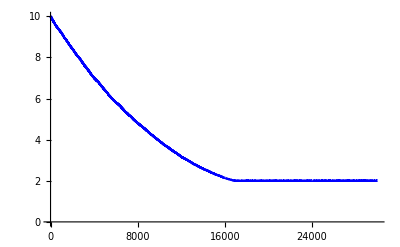

```mathematica
(*Plotte die Resultate*)
burnin =20000;
(*Bestimme die Parameter als Mittelwert der Samplings nach dem burn in*)
m=Mean[Table[samples[[i,1]],{i,burnin,samplesize}]];
b=Mean[Table[samples[[i,2]],{i,burnin,samplesize}]];
(*Bestimme den Fehler anhand dessen, wo 68.3% der Daten liegen*)
median =Median[Table[samples[[i,1]],{i,burnin,samplesize}]];
liste=Table[ Abs[samples[[i,1]]-median],{i,burnin,samplesize}];
Sort[liste];
om=liste[[Round[Length[liste]*0.683]]];

median =Median[Table[samples[[i,2]],{i,burnin,samplesize}]];
liste=Table[ Abs[samples[[i,2]]-median],{i,burnin,samplesize}];
Sort[liste];
ob=liste[[Round[Length[liste]*0.683]]];
(*Bestimme die Quantile*)
qm=Quantile[Table[samples[[i,1]],{i,burnin,samplesize}],{0.25,0.5,0.75}];
qb=Quantile[Table[samples[[i,2]],{i,burnin,samplesize}],{0.25,0.5,0.75}];


(*Plotte die Resultate*)
Histogram[Table[samples[[i,1]],{i,burnin,samplesize}],Automatic,"Probability",PlotLabel->"Histogram m"]
Histogram[Table[samples[[i,2]],{i,burnin,samplesize}],Automatic,"Probability",PlotLabel->"Histogram b"]
Histogram3D[Table[{samples[[i,1]],samples[[i,2]]},{i,burnin,samplesize}],Automatic,"Probability",PlotLabel->"Histogram m-b",AxesLabel-> {"m","b"}]
Print["m = ",m," +- ",om];
Print["b = ",b," +- ",ob];
RMS=√((∑_(i=1)^n (Y[[i]]-y[X[[i]]])^2)/(n-u));
Print["RMS: ",RMS];
Print["m Quantile: ",qm];
Print["qm_3/4 - qm_1/4 = ",qm[[3]]-qm[[1]]];
Print["b Quantile: ",qb];
Print["qb_3/4 - qb_1/4 = ",qb[[3]]-qb[[1]]];
Print["Blau: Modell, Grün: Daten, Rot: Residuen"]
Show[Plot[y[x],{x,-(n-1)/2,(n-1)/2},PlotStyle->Blue],ErrorListPlot[Table[{{X[[i]],Y[[i]]},ErrorBar[0.5]},{i,1,n}],PlotStyle-> Green],ListLinePlot[Table[{X[[i]],Y[[i]]-y[X[[i]]]},{i,1,n}],PlotStyle-> Red],AxesLabel-> {"x","y"}]
```

## Uniform-Verteilung

```mathematica
(*Definiere den ln der Funktion f = Likelihood*Prior *)
lnf[theta_]:=(
y[x_]:=theta[[1]]*x+theta[[2]];
Prior = 1/(3-1)*1/(0-(-2));
lnL = -n/2 Log[2π*0.5^2]-1/(2*0.5^2)∑_(i=1)^n (y[X[[i]]]-Y[[i]])^2;
Return[lnL+Log[Prior]];)
(*q: Proposal Funktion*)
om= 0.0007;
ob = 0.0007;

qm[theta_]:=(us = RandomReal[];Return[2 om us +theta -om]);
qb[theta_]:=(us = RandomReal[];Return[2 ob us +theta -ob]);


(*Bestimme die samples*)
samplesize = 1000000;

Rate ={0,0};
theta1 = {0,0};
theta2 = {0,0};
samples= Table[0,samplesize];
switch = 0;

Do[theta2[[1]] = qm[theta1[[1]]];
r = RandomReal[];
If[lnf[theta2]-lnf[theta1]>Log[r],theta1[[1]] = theta2[[1]];Rate[[1]]+=1];

theta2[[2]] = qb[theta1[[2]]];
r = RandomReal[];
If[lnf[theta2]-lnf[theta1]>Log[r],theta1[[2]] = theta2[[2]];Rate[[2]]+=1];

samples[[i]]=theta1;

(*Passe die Breite an*)
If[switch == 0 && Mod[i,1000]==0,
If[Rate[[1]]  < 600 ,om -= 0.00001];
If[Rate [[1]] > 800,om+= 0.00001];
If[Rate[[2]]  < 600 ,ob -= 0.00001];
If[Rate [[2]] > 800,ob+= 0.00001];
If[Min[Rate]≥ 600&&Max[Rate]≤ 800,switch = 1;Print["Daten können ab dem ",i,". Schritt genutzt werden."];Print[" "]];
Rate = {0,0}],

{i,1,samplesize}];

(*Bestimme die Akzeptanzrate*)
Rate = Rate/samplesize*100;


(*Plotte die Samplings*)
Print["Blau: m    Grün: b"];
Show[ListLinePlot[Table[{i,samples[[i,1]]},{i,1,samplesize}],PlotStyle-> Blue],ListLinePlot[Table[{i,samples[[i,2]]},{i,1,samplesize}],PlotStyle-> Green],PlotRange-> All,AxesOrigin-> {0,0}]
Print[" "];
(*Drucke die Resultate aus*)
Print["Akzeptansrate m: ",N[Rate[[1]]],"%"];
Print["Akzeptansrate b: ",N[Rate[[2]]],"%"];
Print["σm: ",om];
Print["σb: ",ob];
```

```mathematica
ListLinePlot[Table[{i,samples[[i,1]]},{i,1,20000}],PlotStyle-> Blue,AxesOrigin->{0,0},PlotRange->All]
ListLinePlot[Table[{i,samples[[i,2]]},{i,1,300000}],PlotStyle-> Green,AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
(*Plotte die Resultate*)
burnin = 200000;
(*Bestimme die Parameter als Mittelwert der Samplings nach dem burn in*)
m=Mean[Table[samples[[i,1]],{i,burnin,samplesize}]];
b=Mean[Table[samples[[i,2]],{i,burnin,samplesize}]];
(*Bestimme den Fehler anhand dessen, wo 68.3% der Daten liegen*)
median =Median[Table[samples[[i,1]],{i,burnin,samplesize}]];
liste=Table[ Abs[samples[[i,1]]-median],{i,burnin,samplesize}];
Sort[liste];
om=liste[[Round[Length[liste]*0.683]]];

median =Median[Table[samples[[i,2]],{i,burnin,samplesize}]];
liste=Table[ Abs[samples[[i,2]]-median],{i,burnin,samplesize}];
Sort[liste];
ob=liste[[Round[Length[liste]*0.683]]];
(*Bestimme die Quantile*)
qm=Quantile[Table[samples[[i,1]],{i,burnin,samplesize}],{0.25,0.5,0.75}];
qb=Quantile[Table[samples[[i,2]],{i,burnin,samplesize}],{0.25,0.5,0.75}];


(*Plotte die Resultate*)
Histogram[Table[samples[[i,1]],{i,burnin,samplesize}],Automatic,"Probability",PlotLabel->"Histogram m"]
Histogram[Table[samples[[i,2]],{i,burnin,samplesize}],Automatic,"Probability",PlotLabel->"Histogram b"]
Histogram3D[Table[{samples[[i,1]],samples[[i,2]]},{i,burnin,samplesize}],Automatic,"Probability",PlotLabel->"Histogram m-b",AxesLabel-> {"m","b"}]
Print["m = ",m," +- ",om];
Print["b = ",b," +- ",ob];
RMS=√((∑_(i=1)^n (Y[[i]]-y[X[[i]]])^2)/(n-u));
Print["RMS: ",RMS];
Print["m Quantile: ",qm];
Print["qm_3/4 - qm_1/4 = ",qm[[3]]-qm[[1]]];
Print["b Quantile: ",qb];
Print["qb_3/4 - qb_1/4 = ",qb[[3]]-qb[[1]]];
Print["Blau: Modell, Grün: Daten, Rot: Residuen"]
Show[Plot[y[x],{x,-(n-1)/2,(n-1)/2},PlotStyle->Blue],ErrorListPlot[Table[{{X[[i]],Y[[i]]},ErrorBar[0.5]},{i,1,n}],PlotStyle-> Green],ListLinePlot[Table[{X[[i]],Y[[i]]-y[X[[i]]]},{i,1,n}],PlotStyle-> Red],AxesLabel-> {"x","y"}]
```

## Nested Sampling

```mathematica
lnL[theta_]:=(
y[x_]:=theta[[1]]*x+theta[[2]];

Return[ -n/2 Log[2π*0.5^2]-1/(2*0.5^2)∑_(i=1)^n (y[X[[i]]]-Y[[i]])^2]);
PriorSampling[x_]:=(u1 = RandomReal[];u2=RandomReal[];Return[{2u1+1,2u2-2}]);

K =500;
epsilon = 10^-6;
livepoints= Table[PriorSampling[0],K];
deadpoints = {};
lnminLlist = {};
lnw = {};

Xi= {};
i = 1;
dlnZi =epsilon+1;

Do[
(*Determine the position of the sample with the smallest Likelihood*)
lnLlist =Table[lnL[livepoints[[i]]],{i,1,K}];
lnLmin = Min[lnLlist];
AppendTo[lnminLlist,lnLmin];
imin = Position[lnLlist,lnLmin][[1,1]];
AppendTo[deadpoints,livepoints[[imin]]];

(*Replace the sample with a new one with a bigger Likelihood*)
test=0;
While[test==0,
sample = PriorSampling[0];
If[lnL[sample] > lnLmin ,livepoints[[imin]] =sample;test=1]];

(*Estimate the Prior Volume*)
AppendTo[Xi,Exp[(-i-√i)/K]];
(*Evaluate Stopping Criterium*)
If[i>1,lnwi = lnLmin+Log[N[Xi[[i-1]]]-N[Xi[[i]]]]];
AppendTo[lnw,lnwi];
maxlnw = Max[lnw];
imax = Position[lnw,maxlnw][[1,1]];
lnZi = maxlnw+Log[1 + Sum[Exp[Delete[lnw,imax][[j]]-maxlnw],{j,1,Length[lnw]-1}]];

lnLmax =Max[lnLlist];
lndZi = lnLmax +(-i-√i)/K;

If[lndZi>lnZi,dlnZi = lndZi+Log[1+Exp[lnZi-lndZi]]-lnZi,dlnZi = lnZi+Log[1+Exp[lndZi-lnZi]]-lnZi];
If[Mod[i,1000]==0,Print[dlnZi]];
i += 1,5000];
```

```mathematica
P = Table[Exp[lnw[[j]]-lnZi],{j,1,Length[lnw]}];
ListPlot[Table[{deadpoints[[j,1]],100*P[[j]]},{j,1,Length[lnw]}],AxesLabel->{"m","P[%]"}]
ListPlot[Table[{deadpoints[[j,2]],100*P[[j]]},{j,1,Length[lnw]}],AxesLabel->{"b","P[%]"}]
ListPointPlot3D[Table[{deadpoints[[j,1]],deadpoints[[j,2]],100*P[[j]]},{j,1,Length[lnw]}],AxesLabel->{"m","b","P[%]"}]
Print["Maximum der Verteilung bei(m,b) = ",deadpoints[[Position[P,Max[P]][[1,1]]]]];
Print["Z: ",Exp[lnZi]];
Print["dZ: ",Exp[dlnZi]];
```

```mathematica
Z=∫_-2^0 ∫_1^3 Exp[lnL[{m,b}]]ⅆmⅆb
```

## Nested Sampling (Binominal)

```mathematica
(*Eine einzige Ziehung*)
n = 1000;
k = 502;
L[p_]:=Binomial[n,k]*p^k*(1-p)^(n-k);
lnL[p_]:=Log[Binomial[n,k]]+k Log[p]+(n-k)Log[1-p];

samplesize = 500;
livepoints = Table[RandomReal[{0.4,0.6}],samplesize];
deadpoints = {};
lnminLlist = {};
lnw = {};
Xi = {};
i = 1;
dlnZi =1;
```

```mathematica
While[dlnZi >10^-3,
(*Determine the position of the sample with the smallest Likelihood*)
lnLlist =Table[lnL[livepoints[[j]]],{j,1,samplesize}];
lnLmin = Min[lnLlist];
AppendTo[lnminLlist,lnLmin];
imin = Position[lnLlist,lnLmin][[1,1]];
AppendTo[deadpoints,livepoints[[imin]]];

(*Replace the sample with a new one with a bigger Likelihood*)
test=0;
While[test==0,
sample = RandomReal[{0.4,0.6}];
If[lnL[sample] > lnLmin ,livepoints[[imin]] =sample;test=1]];

(*Estimate the Prior Volume*)
AppendTo[Xi,Exp[(-i-√i)/samplesize]];
(*Evaluate the importance weight*)

If[i==1,lnwi =lnminLlist[[i]]-Log[2]+Log[(1-Xi[[i]])/2]];
If[i==2,lnwi =lnminLlist[[i]]+Log[1+Exp[lnminLlist[[i-1]]-lnminLlist[[i]]]]-Log[2]+Log[(1-Xi[[i]])/2]];
If[i>2,lnwi =lnminLlist[[i]]+Log[1+Exp[lnminLlist[[i-1]]-lnminLlist[[i]]]]-Log[2]+Log[(Xi[[i-2]]-Xi[[i]])/2]];
AppendTo[lnw,lnwi];

(*Evaluate Stopping Criterium*)

maxlnw = Max[lnw];
imax= Position[lnw,maxlnw][[1,1]];
If[i==1,lnZi=maxlnw];
If[i>1,lnZi =maxlnw +Log[1+∑_(j=1)^(Length[lnw]-1) Exp[Delete[lnw,imax][[j]]-maxlnw]]];

lndZi = Max[lnLlist]+(-i-√i)/samplesize;

dlnZi = lndZi + Log[1+Exp[lnZi-lndZi]]-lnZi;

If[Mod[i,1000]==0,Print[dlnZi]];
i += 1];
```

```mathematica
Print["Z Sampling: ",Exp[lnZi]," + ",Exp[lndZi]];
Print["Z analytisch: ",N[∫_0.4^0.6 L[p]ⅆp]];
```

```mathematica
Z =N[∫_0.4^0.6 L[p]ⅆp];
Plot[L[p]/Z,{p,0.4,0.6},PlotRange->All]

ListPlot[Table[{deadpoints[[j]],Exp[lnw[[j]]]/Exp[lnZi]},{j,1,Length[lnw]}]]
```

```mathematica
ListLinePlot[deadpoints]
```

```mathematica
∫_0.4^0.6 L[p]/Z pⅆp
mittelwert=Sum[Exp[lnw[[j]]]/Exp[lnZi]*deadpoints[[j]],{j,1,Length[lnw]}]
```

```mathematica
∫_0.4^0.6 L[p]/Z p^2 ⅆp-(∫_0.4^0.6 L[p]/Z pⅆp)^2
Sum[(deadpoints[[j]]-mittelwert)^2 Exp[lnw[[j]]]/Exp[lnZi],{j,1,Length[deadpoints]}]
```

```mathematica
(*K = 2'000*)
```

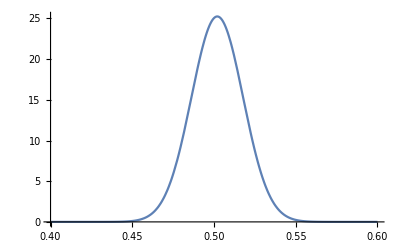

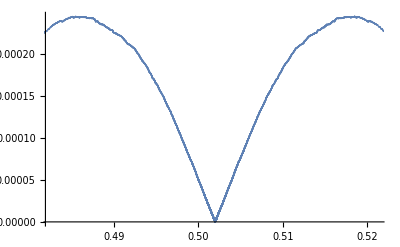

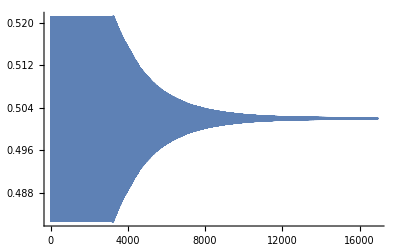

```mathematica
(*Mittelwert*)
0.5019960079692284
0.5021613806277577

(*Varianz*)
0.0002492482689613884
0.00024840890579087203
```